## Generate Fermion Profile Parameters (cL, cR)

Goal: 
	
	
Input: 
	
	
Output:

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]~StringJoin~".."]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

WARNING! DO NOT EVALUATE THE WHOLE NOTEBOOK!

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

For lepton data, separate Yukawa matrices and corresponding r13, r23

```mathematica
leptonDataAll = <<"output/yukawa_lepton.m";
leptonData =leptonDataAll[[All,1;;2]];
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{1030,2,3,3}

### Find a set of c_P, c_M, convert to c_L, c_R

WARNING! THESE RESULTS HAVE BEEN SAVED! 
DO NOT EVALUATE AGAIN

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all quarks 
	for different values of cM
	store in cuData, cdData
 *)
```

```mathematica
(* Common cM value for all arrays *)
cMArray=Range[-6.25,6.25,0.5];
```

```mathematica
With[{seed=0.4},
cuData={};
cdData={};
Do[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[yu];myd=Minors[yd];
AppendTo[cuData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffYukawa[yu,yd,myu,myd][#],{cP,Norm[cM]+seed}]&)/@{"u","c","t"}],
{cM,cMArray}
]//Quiet
];
AppendTo[cdData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffYukawa[yu,yd,myu,myd][#],{cP,Norm[cM]+seed}]&)/@{"d","s","b"}],
{cM,cMArray}
]//Quiet
],{i,Length[quarkData]}
]
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[cuData]
Dimensions[cdData]
```

{240.981,Null}

{1321,26,3,2}

{1321,26,3,2}

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all leptons
	for different values of cM
	store in clNHData, clIHData
 *)
```

```mathematica
With[{seed=0.4},
ceData={};
Do[
yn = leptonData[[i, 1]]; ye = leptonData[[i,2]];myn=Minors[yn];mye=Minors[ye];
AppendTo[ceData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==LeptonEffYukawa[yn,ye,myn,mye][#],{cP,Norm[cM]+seed}]&)/@{"e","mu","tau"}],
{cM,cMArray}
]//Quiet
],{i,Length[leptonData]}]
];//AbsoluteTiming
Clear[yn,ye,myn,mye];
Dimensions[ceData]
```

{96.9039,Null}

{1030,26,3,2}

```mathematica
(* Export all evaluated result *)
```

```mathematica
Export["output/cLcR04.m",{cMArray,cuData,cdData,ceData}]
```

output/cLcR04.m

```mathematica
(* Sanity check *)
```

```mathematica
data= Import["output/cLcR04.m"];
```

```mathematica
{cMArray,cuData,cdData,ceData}=data;
```

```mathematica
Dimensions[cuData]
```

{1321,41,3,2}

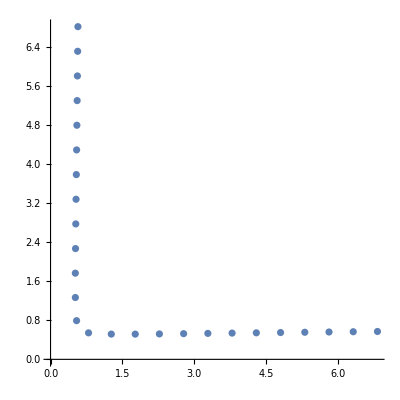

```mathematica
ListPlot[cuData[[3,All,3,All]],AspectRatio->1]
```

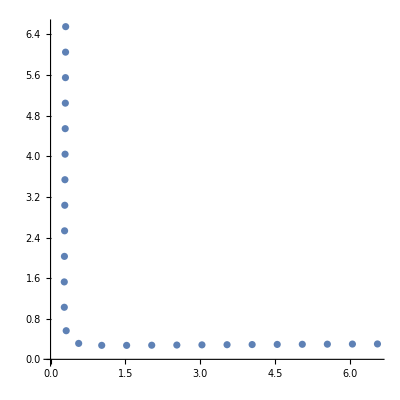

```mathematica
ListPlot[cdData[[3,All,3,All]],AspectRatio->1]
```

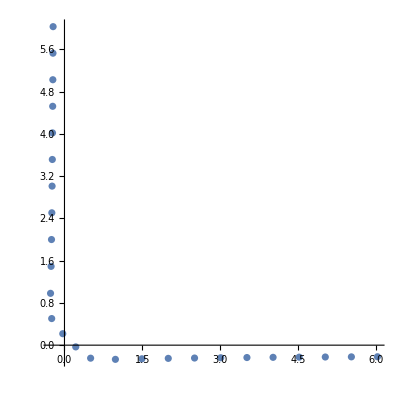

```mathematica
ListPlot[ceData[[1,All,1,All]],AspectRatio->1]
```